```mathematica
ClearAll["`*"]
L=1;m^2=-2;
```

## eigen equation

```mathematica
vars={t,z,x,y};xa[μ_]:=vars⟦μ⟧;dim=Length[vars];
f[z_]:=1-(1+mubar^2/(4 zh^2)) z^3+mubar^2/(4 zh^2)z^4;
ds^2=zh^2/z^2(-f[z] Dt[t]^2+Dt[z]^2/(zh^2 f[z])+Dt[x]^2+Dt[y]^2);
coematrix=Coefficient[ds^2,Dt[vars]⊗Dt[vars]];
metric=1/2 Simplify[coematrix+DiagonalMatrix[Diagonal[coematrix]]];
gbb[μ_,ν_]:=metric⟦μ,ν⟧;
invmetric=Simplify[Inverse[metric]];
gaa[μ_,ν_]:=invmetric⟦μ,ν⟧;
g=Simplify[Det[metric]];
Γabb[λ_,μ_,ν_]:=Simplify[∑_(σ=1)^dim 1/2 gaa[λ,σ] (-D[gbb[μ,ν], xa[σ]]+D[gbb[ν,σ], xa[μ]]+D[gbb[σ,μ], xa[ν]])];
(*ansatz for scalar field*)
Φ=(z/zh) ϕ[z];
A={mubar/(√e)(1-z),0,0,0};
Ab[μ_]:=A⟦μ⟧;Aa[ν_]:=∑_(σ=1)^dim gaa[σ,ν] Ab[σ];
DΦb[μ_]:=D[Φ, xa[μ]]-ⅈ Ab[μ]Φ;
scalar=Simplify[1/(√-g)∑_(μ=1)^dim (D[#, xa[μ]]-ⅈ Ab[μ]#&[√-g ∑_(ν=1)^dim gaa[μ,ν] DΦb[ν]])-m^2 Φ];
nonfactor[eqs_]:=Block[{First,Last,FactorList},SetAttributes[{First,Last,FactorList},Listable];Simplify[First[Last[FactorList[eqs]]]]];
eqs=Collect[Simplify[scalar//nonfactor],zh,Simplify]
Collect[Simplify[scalar//nonfactor],zh,Simplify];
jacobi=Simplify[Coefficient[(eqs/.{Derivative[i_][h_][z]->Subscript[dz, i] h[z],h_[z]->eye h[z]}),ϕ[z]]];
Collect[jacobi,zh,Simplify]
subeqs=eqs/.{Derivative[i_][h_][z]:>D[(Series[h[z],{z,1,3}]), {z,i}],h_[z]:>Series[h[z],{z,1,3}]};
```

16 e (1+z+z^2) zh^4 (z ϕ[z]+3 z^2 ϕ'[z]+(-1+z^3) ϕ''[z])+e mubar^4 z^4 ((-1+2 z) ϕ[z]+z ((-3+4 z) ϕ'[z]+(-1+z) z ϕ''[z]))+4 mubar^2 zh^2 (-(4-(4+e) z+e z^2+e z^3+3 e z^4) ϕ[z]-e z^2 ((-3+z+z^2+7 z^3) ϕ'[z]+2 z (-1+z^3) ϕ''[z]))

e mubar^4 z^4 (eye (-1+2 z)+z (-3+4 z) dz_1+(-1+z) z^2 dz_2)+16 e (1+z+z^2) zh^4 (eye z+3 z^2 dz_1+(-1+z^3) dz_2)+4 mubar^2 zh^2 (-eye (4-(4+e) z+e z^2+e z^3+3 e z^4)-e z^2 (-3+z+z^2+7 z^3) dz_1-2 e z^3 (-1+z^3) dz_2)

```mathematica
X=Simplify[Coefficient[jacobi,zh^4]]
Y=Simplify[Coefficient[jacobi,zh^2]]
Z=Simplify[jacobi/.zh->0]
Simplify[SeriesCoefficient[subeqs,{z,1,0}]]
Simplify[SeriesCoefficient[eqs,{z,1,0}]]
```

16 e (1+z+z^2) (eye z+3 z^2 dz_1+(-1+z^3) dz_2)

-4 mubar^2 (eye (4-(4+e) z+e z^2+e z^3+3 e z^4)+e z^2 (-3+z+z^2+7 z^3) dz_1+2 e z^3 (-1+z^3) dz_2)

e mubar^4 z^4 (eye (-1+2 z)+z (-3+4 z) dz_1+(-1+z) z^2 dz_2)

e (mubar^2-12 zh^2) (mubar^2 (ϕ[1]+ϕ'[1])-4 zh^2 (ϕ[1]+3 ϕ'[1]))

e (mubar^2-12 zh^2) (mubar^2 (ϕ[1]+ϕ'[1])-4 zh^2 (ϕ[1]+3 ϕ'[1]))

## eigenvalue

```mathematica
Nz=36;Lz=1;mubar=5.6;e=1/1.1112567054294926;
(*Chebshev谱求导矩阵生成函数*)
chebp[n_]:=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,1,n}];sdm=2/l Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];
Eye=IdentityMatrix[Nz];Zero=ConstantArray[0,{Nz,Nz}];
gridz=0.5(chebp[Nz]+1);
dz=cheb[Nz,Lz];dzs[1]=dz;dzs[2]=dz.dz;
{Xm,Ym,Zm}={X,Y,Z}/.{Subscript[dz, i_]->dzs[i],eye->Eye,z-> gridz};
Xm⟦1⟧=Zero⟦1⟧;Xm⟦-1⟧=Zero⟦-1⟧;
Ym⟦1⟧=-4(Eye⟦1⟧+3dz⟦1⟧);Ym⟦-1⟧=Zero⟦-1⟧;
Zm⟦1⟧=mubar^2(Eye⟦1⟧+dz⟦1⟧);Zm⟦-1⟧=dz⟦-1⟧;
left=ArrayFlatten[{{-Ym,-Zm},{Eye,Zero}}];
right=ArrayFlatten[{{Xm,Zero},{Zero,Eye}}];
EV=Chop[Eigenvalues[{left,right}]]
EVmax=Max[Abs[DeleteCases[DeleteCases[Chop[Eigenvalues[{left,right}]],∞],ComplexInfinity]]]
1/mubar(zh/(4π)(3- mubar^2/(4 zh^2)))/.zh->√EVmax
```

{ComplexInfinity,ComplexInfinity,ComplexInfinity,29.9626,2.78674,2.61981,2.6004+0.00565811 ⅈ,2.6004-0.00565811 ⅈ,2.59261,2.54706,2.52492,2.48637,2.46894,2.39201,2.36194,2.29383,2.26989,2.16423,2.13139,2.03537,2.01141,1.87961,1.85101,1.73009,1.71149,1.55822,1.54066,1.40245,1.38853,1.2226+0.00252765 ⅈ,1.2226-0.00252765 ⅈ,1.08126,1.05985,0.914533,0.901245,0.786006,0.751295,0.641533,0.611766,0.531963,0.486535,0.415652,0.37535,0.330314,0.280882,0.244751,0.202022,0.184772,0.13953,0.128245,0.0911249+0.000509092 ⅈ,0.0911249-0.000509092 ⅈ,0.0583903,0.0562898,0.0380715,0.0324364,0.0219754,0.0170585,0.0129287,0.00805845,0.00640328,0.00329478,0.00323103,0.00119976,0.00110988,0.000408771,0.00030138,0.0000572769,6.79625×10^-6,3.75074×10^-7,5.60559×10^-9,0}

29.9626

0.213

## evstc

### bcs-like

```mathematica
Nz=56;Lz=1;mubar=5.6;evstclist2={};
(*Chebshev谱求导矩阵生成函数*)
chebp[n_]:=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,1,n}];sdm=2/l Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];
Eye=IdentityMatrix[Nz];Zero=ConstantArray[0,{Nz,Nz}];
gridz=0.5(chebp[Nz]+1);
dz=cheb[Nz,Lz];dzs[1]=dz;dzs[2]=dz.dz;
Do[{Xm,Ym,Zm}={X,Y,Z}/.{Subscript[dz, i_]->dzs[i],eye->Eye,z-> gridz};
Xm⟦1⟧=Zero⟦1⟧;Xm⟦-1⟧=Zero⟦-1⟧;
Ym⟦1⟧=-4(Eye⟦1⟧+3dz⟦1⟧);Ym⟦-1⟧=Zero⟦-1⟧;
Zm⟦1⟧=mubar^2(Eye⟦1⟧+dz⟦1⟧);Zm⟦-1⟧=Eye⟦-1⟧;
left=ArrayFlatten[{{-Ym,-Zm},{Eye,Zero}}];
right=ArrayFlatten[{{Xm,Zero},{Zero,Eye}}];
EV=Chop[Eigenvalues[{left,right}]];
EVmax=Max[Abs[Cases[Chop[Eigenvalues[{left,right}]],p_/;NumberQ[p]]]];
tc=(√e)/mubar(zh/(4π)(3- mubar^2/(4 zh^2)))/.zh->√EVmax;
AppendTo[evstclist2,{e,tc}],{e,0.1,1,0.05}]
```

```mathematica
evstclist2
```

{{0.1,0.0528588},{0.15,0.0501256},{0.2,0.0475279},{0.25,0.0450615},{0.3,0.0427221},{0.35,0.0405054},{0.4,0.038407},{0.45,0.0364222},{0.5,0.0345465},{0.55,0.0327752},{0.6,0.0311038},{0.65,0.0295277},{0.7,0.0280422},{0.75,0.026643},{0.8,0.0253254},{0.85,0.0240854},{0.9,0.0229185},{0.95,0.0218209},{1.,0.0207884}}

### bec-like

```mathematica
Nz=36;Lz=1;mubar=5.6;evstclist1={};
(*Chebshev谱求导矩阵生成函数*)
chebp[n_]:=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,1,n}];sdm=2/l Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];
Eye=IdentityMatrix[Nz];Zero=ConstantArray[0,{Nz,Nz}];
gridz=0.5(chebp[Nz]+1);
dz=cheb[Nz,Lz];dzs[1]=dz;dzs[2]=dz.dz;
Do[{Xm,Ym,Zm}={X,Y,Z}/.{Subscript[dz, i_]->dzs[i],eye->Eye,z-> gridz};
Xm⟦1⟧=Zero⟦1⟧;Xm⟦-1⟧=Zero⟦-1⟧;
Ym⟦1⟧=-4(Eye⟦1⟧+3dz⟦1⟧);Ym⟦-1⟧=Zero⟦-1⟧;
Zm⟦1⟧=mubar^2(Eye⟦1⟧+dz⟦1⟧);Zm⟦-1⟧=dz⟦-1⟧;
left=ArrayFlatten[{{-Ym,-Zm},{Eye,Zero}}];
right=ArrayFlatten[{{Xm,Zero},{Zero,Eye}}];
EV=Chop[Eigenvalues[{left,right}]];
EVmax=Max[Abs[Cases[Chop[Eigenvalues[{left,right}]],p_/;NumberQ[p]]]];
tc=(√e)/mubar(zh/(4π)(3- mubar^2/(4 zh^2)))/.zh->√EVmax;
AppendTo[evstclist1,{e,tc}],{e,0.1,1,0.05}]
```

```mathematica
evstclist1
```

{{0.1,0.211771},{0.15,0.211128},{0.2,0.21049},{0.25,0.209857},{0.3,0.209229},{0.35,0.208606},{0.4,0.207987},{0.45,0.207374},{0.5,0.206764},{0.55,0.20616},{0.6,0.20556},{0.65,0.204964},{0.7,0.204374},{0.75,0.203787},{0.8,0.203205},{0.85,0.202628},{0.9,0.202055},{0.95,0.201486},{1.,0.200922}}

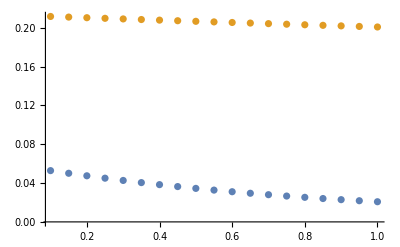

```mathematica
ListPlot[{evstclist2,evstclist1},PlotRange->All]
```